```mathematica
Px0[x_,s_]=1/(2 s)(HeavisideTheta[x+s]-HeavisideTheta[x-s] )
Pv0[v_,vth_]=1/(√(2 π vth^2))ⅇ^(-v^2/(2 vth^2));
P0[x_,v_,s_,vth_]= Px0[x,s]Pv0[v,vth];
V0[x_,s_]=Integrate[D[FullSimplify[-Log[Px0[x,s]],Assumptions->{s>0}],x],x]
```

(-HeavisideTheta[-s+x]+HeavisideTheta[s+x])/(2 s)

-Log[HeavisideTheta[-s+x]-HeavisideTheta[s+x]]

```mathematica
Pxslice[x_,t_,s_,vth_,v0_,a_,b_]=FullSimplify[
Pv0[0,vth]Px0[0,s]Integrate[ⅇ^(-( v^2/(2 vth^2))),{v,-v0+(x-b)/t,-v0 +(x-a)/t},
Assumptions->{s>0,vth>0,t>0,b>a, v0>0, a>-s,b<s}] ,Assumptions->{s>0,vth>0,t>0,b>a, x ∈Reals}]
```

(-Erf[(a+t v0-x)/(√2 t vth)]+Erf[(b+t v0-x)/(√2 t vth)])/(4 s)

```mathematica
Integrate[x^2 Pxslice[x,t,s,vth,-mJ γ vth,s(2mJ-1)/(2 J+1) ,s(2mJ +1)/(2 J +1)],{x,-∞,∞},Assumptions->{s>0,vth>0,t>0, γ>0, δ>0,J>0, mJ∈Reals}]
```

((1+12 mJ^2) s^2-12 (1+2 J) mJ^2 s t vth γ+3 (1+2 J)^2 t^2 vth^2 (1+mJ^2 γ^2))/(3 (1+2 J)^3)

```mathematica
flatvar[t_,γ_,J_,s_]=FullSimplify[Sum[((1+12 mJ^2) s^2-12 (1+2 J) mJ^2 s t vth γ+3 (1+2 J)^2 t^2 vth^2 (1+mJ^2 γ^2))/(3 (1+2 J)^3),{mJ,-J,J,1}],Assumptions->{s>0,vth>0,t>0, γ>0, J>0}]
```

((1+2 J) s^2-4 J (1+J) s t vth γ+(1+2 J) t^2 vth^2 (3+J (1+J) γ^2))/(3+6 J)

```mathematica
Solve[D[FullSimplify[flatvar[t,γ,J,s]/(s^2/3),Assumptions->{s>0}], t] == 0,t]//FullSimplify
```

{{t→(2 J (1+J) s γ)/((1+2 J) vth (3+J (1+J) γ^2))}}

```mathematica
Series[(2 J (1+J) s γ)/((1+2 J) vth (3+J (1+J) γ^2)),{γ,∞,1}]
```

(2 s)/((1+2 J) vth γ)+O[1/γ]^2

```mathematica
FullSimplify[flatvar[t,γ,J,s]/(s^2/3),Assumptions->{s>0,vth>0,t>0, γ>0, J>0}]
```

1-(4 J (1+J) t vth γ)/(s+2 J s)+(t^2 vth^2 (3+J (1+J) γ^2))/s^2

```mathematica
FullSimplify[s/(√3)/√flatvar[(2 J (1+J) s γ)/((1+2 J) vth (3+J γ^2+J^2 γ^2)),γ,J,s],Assumptions->{s>0,vth>0,t>0, γ>0, J>0}]
```

(1+2 J) √((3+J (1+J) γ^2)/(3+J (1+J) (12+γ^2)))

```mathematica
FullSimplify[s/(√3)/√flatvar[(2 s)/((1+2 J) vth γ),γ,J,s],Assumptions->{s>0,vth>0,t>0, γ>0, J>0}]
```

(γ+2 J γ)/(√(12+γ^2))

```mathematica
Sqrt[12.]
```

3.4641

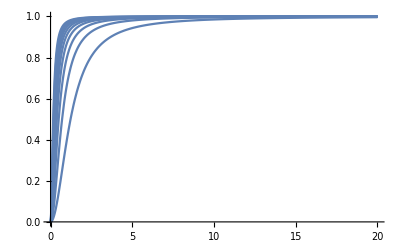

```mathematica
Plot[Table[((2 J (1+J)  γ)/((1+2 J)  (3+J (1+J) γ^2)))/(2/((1+2 J)  γ)),{J,1,10,1}],{γ,0,20}, PlotRange->All]
```